# QFT compilation

## Toy device

Connectivity

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

Modules

```mathematica
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]
```

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_,list_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits},

{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];
AppendTo[list,{conf,time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}];

nansatz=noisyAnsatz[ansatz/.θvars,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=1-CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

## 3 qubit QFT

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

## Clean device

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

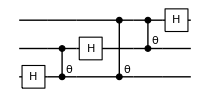

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

Finite difference

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy0={};
Table[
conf=checkedConf[dev,unitary,5];
CompileCirc[conf,unitary,qubitsnum,toy0]
,{5}];
```

Compilation with automatically generated ansatz

@cycle1:Fri 16 Sep 2022 22:45:50, fev:149, <E>: 0.3105969081365281 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 1, 6}

$Aborted

## Small error: gate fidelity: 0.9999, T1=10^5,T2=100

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->100,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.9999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.9999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->1
};
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy1={};
Table[
conf=checkedConf[dev,unitary,5];
CompileCirc[conf,unitary,qubitsnum,toy1]
,{5}];
```

## Mid error : 0.999, T1=10^5,T2=40

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->5
};
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy2={};
Table[
conf=checkedConf[dev,unitary,5];
CompileCirc[conf,unitary,qubitsnum,toy2]
,{5}];
```

## Severe error : 0.99, T1=10^5,T2=20

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.99,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.99,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->5
};
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy3={};
Table[
conf=checkedConf[dev,unitary,5];
CompileCirc[conf,unitary,qubitsnum,toy3]
,{5}];
```